# LISA MBHBs vs Quasars

### Settings:

Choose number of MBHB standard sirens :

```mathematica
nSS=Range[10,50,5]
```

{10,15,20,25,30,35,40,45,50}

Choose number of realizations :

```mathematica
nrel=3;
```

The code below will create nrel different catalogs each containing nSS standard sirens and produce results averaged over all catalogs.

Choose fiducial value of nSS (must be one of the values of nSS)

```mathematica
fiducialnSS=15;
```

```mathematica
fiducialk=Position[nSS,fiducialnSS]⟦1,1⟧;
```

Set confidence level for plotting:

```mathematica
CL=0.9;
```

Setting random seed for reproducibility

```mathematica
ranseed=17;
SeedRandom[ranseed]
```

Step for saving curves in z

```mathematica
nstep=.01;
```

#### Saving inputs file

Need first to create folder “output/” in notebook’s folder

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["output/input_settings.txt","
nSS = "<>ToString[nSS]<>"
nrel = "<>ToString[nrel]<>"
fiducialnSS = "<>ToString[fiducialnSS]<>"
CL = "<>ToString[CL]<>"
RandomSeed = "<>ToString[ranseed]<>"
"];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/input_settings.txt.

#### Silencing warning messages

Turn off message errors for fit (warning about Gaussian approximation hitting the priors on cosmo parameters)

```mathematica
(*Off[FittedModel::constr]*)
ParallelEvaluate[Off[FittedModel::constr]];
```

### Selecting redshift values from redshift distribution in Figure 1 of 1612.02634

Distribution of MBHBs by redshift (see Figure 1 of Tamanini, 1612.02634) - here popIII model chosen

```mathematica
(*dndztabQ3nd ={{0.5,3.75},{1.5,10.25},{2.5,9.25},{3.5,7.75},{4.5,5},{5.5,2.75},{6.5,1.25},{7.5,0.5},{8.5,0.25}};*)
dndztabpop3 ={{0.5,2},{1.5,7},{2.5,8},{3.5,5.25},{4.5,3.25},{5.5,1.5},{6.5,0.5},{7.5,0.25},{8.5,0}};
```

```mathematica
dndztab =Join[{{0,0}},dndztabpop3,{{9.5,0},{10,0}}];
```

Create a probability function by interpolation

```mathematica
Clear[fprob]
fprob[x_]=Piecewise[{{Max[0,Interpolation[dndztab][x]],0.1<x<10}},0];
```

Creating a probability distribution:

```mathematica
dist=ProbabilityDistribution[fprob[x],{x,0,10},Method->"Normalize"];
(*Plot[PDF[%,x],{x,0,10}]*)
```

Creating nrel catalogs by drawing nSS redshifts from distribution:

```mathematica
Clear[zSS]
For[i=1,i≤Length[nSS],i++,
For[j=1,j≤nrel,j++,
zSS[i][j]=RandomVariate[dist,nSS⟦i⟧]
]]
```

### Estimating distance uncertainties

Luminosity Distance equations for LCDM

```mathematica
(* Constants *)
cMKS=2.99792458 10^5;(*in km/sec*)
H100=100 10^-6;(* in km s^-1 pc^-1 *)
```

```mathematica
H[z_,Ωm_,h_] := H100 h Sqrt[Ωm(1+z)^3 + (1-Ωm)]
```

```mathematica
DL[z_,Ωm_,h_] :=cMKS(1+z)NIntegrate[1/H[x,Ωm,h],{x,0,z}] (* in pc *)
```

Derivative of D_Lin redshift

```mathematica
DerivDLz[z_,Ωm_,h_]:=cMKS( NIntegrate[1/H[x,Ωm,h],{x,0,z}]+(1+z)/H[z,Ωm,h])
```

Fiducial LCDM values:

```mathematica
Ωmref=0.3;
href=0.7;
```

Distances to MBHBs from drawn redshift values

```mathematica
Clear[dLSS]
For[i=1,i≤Length[nSS],i++,
For[j=1,j≤nrel,j++,
dLSS[i][j]=ParallelTable[DL[zSS[i][j]⟦k⟧,Ωmref,href],{k,nSS⟦i⟧}]
]]
```

DL weak-lensing relative uncertainty:  equation (22) of DOI: 10.1103/PhysRevD.81.124046 (no delensing)

```mathematica
σlensNDL[z_] :=0.066((1-(1+z)^-0.25)/0.25)^1.8
```

Apply expected de-lensing: from 0907.3635 de-lensing can conservatively be ~30% at z=2, after that it remain roughly constant. Since at z=0 de-lensing must be zero we will assume the following de-lensing fit:

```mathematica
zstarDL=NSolve[(1-0.3/(π/2)ArcTan[2/bb])==0.7*1.01,bb]⟦1,1,2⟧;
delens[z_]:=(1-0.3/(π/2)ArcTan[z/zstarDL])
σlens[z_]:=delens[z]σlensNDL[z]
```

```mathematica
(*Plot[{σlensNDL[z],σlens[z]},{z,0,10}]*)
```

Peculiar velocity uncertainty

```mathematica
σv[z_] := (1+(cMKS(1+z)^2)/(H[z,Ωmref,href]DL[z,Ωmref,href]))500/cMKS
```

LISA instrument relative uncertainty: from 2003.00357 assuming SNR inversely proportional to dL + factor of 2 for marginalizing over inclination (see doi:10.1007/978-3-319- 19273-4; eq. (12.8))

```mathematica
σLISA[z_]:=2 0.1/4 DL[z,0.3,0.7]/(36.6 10^9);
```

Redshift photometric uncertainty (from DOI: 10.1088/1475-7516/2016/04/002)

```mathematica
σzphoto[z_]:=0.03(1+z)
```

```mathematica
σphotoredshift[z_]:=If[z≥2,σzphoto[z]DerivDLz[z,Ωmref,href]/DL[z,Ωmref,href],0]
```

Total relative error

```mathematica
σtot[z_]:=Sqrt[σlens[z]^2+σLISA[z]^2+σv[z]^2+σphotoredshift[z]^2];
```

Plotting error contribution:

```mathematica
(*LogLinearPlot[{σlensNDL[z],σlens[z],σv[z],σLISA[z],σphotoredshift[z],σtot[z]},{z,0.1,10},
Frame->True,FrameLabel->{"z","1σ relative uncertainties"},FrameStyle->Directive[20,FontFamily->"Times"],
PlotStyle->{{Red,Dotted},Red,Orange,Blue,Darker[Green],{Black,Dashed}},
(*PlotRange->{0,.16},*)
PlotLegends->Placed[LineLegend[{"lensing (no delensing)","lensing (with delensing)","peculiar velocities","LISA measurement","redshift measurement","total (with delensing)"},LegendLabel->"Distance error contributions:",LabelStyle->Directive[15,FontFamily->"Times"]],{.25,.64}],
ImageSize->500]
SetDirectory[NotebookDirectory[]];*)
```

Total absolute DL errors (if z>2 photometric redshift uncertainty added):

```mathematica
σtotabs[z_]:=Sqrt[σlens[z]^2+σv[z]^2+σLISA[z]^2+σphotoredshift[z]^2]DL[z,Ωmref,href]
```

Creating error data

```mathematica
Clear[σSS]
For[k=1,k≤Length[nSS],k++,For[j=1,j≤nrel,j++,σSS[k][j]=ParallelTable[Sqrt[σlens[zSS[k][j]⟦i⟧]^2+σv[zSS[k][j]⟦i⟧]^2+σLISA[zSS[k][j]⟦i⟧]^2+σphotoredshift[zSS[k][j]⟦i⟧]^2]dLSS[k][j]⟦i⟧,{i,nSS⟦k⟧}]
]]
```

### Creating standard sirens data

Scattering DL data:

```mathematica
Clear[dLSSscat]
For[k=1,k≤Length[nSS],k++,For[j=1,j≤nrel,j++,
dLSSscat[k][j]=ParallelTable[RandomVariate[NormalDistribution[dLSS[k][j]⟦i⟧,σSS[k][j]⟦i⟧]],{i,nSS⟦k⟧}]]]
```

Check for negative distances (if scattered dL goes negative)

```mathematica
If[Length[Select[Flatten[Table[dLSSscat[k][j],{k,Length[nSS]},{j,nrel}]],#<0&]]≠0,Print["NEGATIVE DISTANCES!!!"]]
```

Data catalogs all redshifts: ( 1.z, 2. D_L[Gpc], 3. ΔD_L[Gpc] )

```mathematica
Clear[dataSS]
For[k=1,k≤Length[nSS],k++,For[j=1,j≤nrel,j++,
dataSS[k][j]=ParallelTable[{zSS[k][j]⟦i⟧,dLSSscat[k][j]⟦i⟧/10^9,σSS[k][j]⟦i⟧/10^9},{i,nSS⟦k⟧}]]]
```

### Fitting

#### Preliminaries for fit

Data for the fit

```mathematica
Clear[pointdata,errdata]
For[k=1,k≤Length[nSS],k++,For[j=1,j≤nrel,j++,
pointdata[k][j]=Table[{zSS[k][j]⟦i⟧,dLSSscat[k][j]⟦i⟧},{i,nSS⟦k⟧}]]]
For[k=1,k≤Length[nSS],k++,For[j=1,j≤nrel,j++,
errdata[k][j]=Table[σSS[k][j]⟦i⟧,{i,nSS⟦k⟧}]]]
```

Some constants

```mathematica
(* Constants *)
cMKS=2.99792458 10^5;(*in km/sec*)
H100=100 10^-6;(* in km s^-1 pc^-1 *)
```

Define numerical function of dL

```mathematica
Clear[DLfit]
DLfit[z_?NumericQ,Ωm_?NumericQ,h_?NumericQ] := (1+z) cMKS/H100 NIntegrate[1/(h Sqrt[Ωm(1+x)^3 + (1-Ωm)]),{x,0,z}] (* in pc *)
```

#### Perform fit

```mathematica
Clear[nlm]
ParallelTable[NonlinearModelFit[pointdata[k][j],{DLfit[z,Ωm,h],{0.04<Ωm<1.,0.<h<1.5}},{{Ωm,.3},{h,.7}},z,Weights->1/(errdata[k][j])^2,VarianceEstimatorFunction->(1&),MaxIterations->50000(*,Method->"Gradient"*)],{k,Length[nSS]},{j,nrel}];
Table[nlm[k][j]=%⟦k,j⟧,{k,Length[nSS]},{j,nrel}];
```

### Confidence intervals

#### Find median fit among all realizations

Computing Fisher matrices

```mathematica
ParallelTable[Inverse[nlm[k][j]["CovarianceMatrix"]],{k,Length[nSS]},{j,nrel}];
Table[FM[k][j]=%⟦k,j⟧,{k,Length[nSS]},{j,nrel}];
```

Computing determinants of FMs

```mathematica
For[k=1,k≤Length[nSS],k++,For[j=1,j≤nrel,j++,detFM[k][j]=Det[FM[k][j]]]]
```

Computing median of determinants

```mathematica
For[k=1,k≤Length[nSS],k++,mediandetFM[k]=Median[Table[detFM[k][j],{j,nrel}]]]
```

Finding FMs with det closer to median

```mathematica
For[k=1,k≤Length[nSS],k++,ord[k]=First[Ordering[Table[N[Abs[detFM[k][j] -mediandetFM[k]]], {j,nrel}]]]]
```

```mathematica
For[k=1,k≤Length[nSS],k++,medianFM[k]=FM[k][ord[k]]]
```

Finding best fit parameters of median realization

```mathematica
Table[medianestparam[k]=nlm[k][ord[k]]["BestFitParameters"],{k,Length[nSS]}];
```

#### Find median best fit parameters and C.I.

Find median fitted values among all realizations

```mathematica
Clear[estΩm,esth]
Table[estΩm[k]=Median[Ωm/.Table[nlm[k][j]["BestFitParameters"],{j,nrel}]],{k,Length[nSS]}];
Table[esth[k]=Median[h/.Table[nlm[k][j]["BestFitParameters"],{j,nrel}]],{k,Length[nSS]}];
```

Find median CL

```mathematica
allCL90=ParallelTable[nlm[k][j]["ParameterConfidenceIntervals",ConfidenceLevel->0.9],{k,Length[nSS]},{j,nrel}];
```

```mathematica
Table[CI90Ωm[k]=Median[(allCL90⟦k,All,1,2⟧-allCL90⟦k,All,1,1⟧)/2],{k,Length[nSS]}];
Table[CI90h[k]=Median[(allCL90⟦k,All,2,2⟧-allCL90⟦k,All,2,1⟧)/2],{k,Length[nSS]}];
```

```mathematica
Table[CI90ΩmLow[k]=Quantile[(allCL90⟦k,All,1,2⟧-allCL90⟦k,All,1,1⟧)/2,.1],{k,Length[nSS]}];
Table[CI90hLow[k]=Quantile[(allCL90⟦k,All,2,2⟧-allCL90⟦k,All,2,1⟧)/2,.1],{k,Length[nSS]}];
```

```mathematica
Table[CI90ΩmHigh[k]=Quantile[(allCL90⟦k,All,1,2⟧-allCL90⟦k,All,1,1⟧)/2,.9],{k,Length[nSS]}];
Table[CI90hHigh[k]=Quantile[(allCL90⟦k,All,2,2⟧-allCL90⟦k,All,2,1⟧)/2,.9],{k,Length[nSS]}];
```

#### Plotting median CLs

```mathematica
datafig=Join[{Table[{nSS⟦k⟧,CI90Ωm[k]},{k,Length[nSS]}]},{Table[{nSS⟦k⟧,CI90h[k]},{k,Length[nSS]}]},
{Table[{nSS⟦k⟧,CI90ΩmLow[k]},{k,Length[nSS]}]},{Table[{nSS⟦k⟧,CI90hLow[k]},{k,Length[nSS]}]},
{Table[{nSS⟦k⟧,CI90ΩmHigh[k]},{k,Length[nSS]}]},{Table[{nSS⟦k⟧,CI90hHigh[k]},{k,Length[nSS]}]}];
```

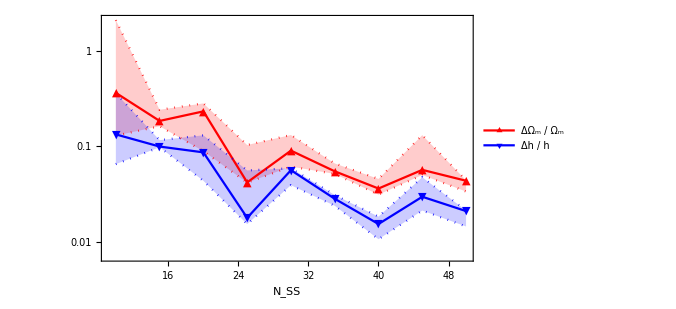

```mathematica
ListLogPlot[datafig,
Frame->True,FrameLabel->{"N_SS",None},FrameStyle->15,ImageSize->500,Joined->True,
PlotMarkers->{"▲","▼","","","",""},GridLines->All,
Filling->{3->{1},4->{2},5->{1},6->{2}},
PlotStyle->{Red,Blue,{Red,Dotted},{Blue,Dotted},{Red,Dotted},{Blue,Dotted}},
PlotLegends->Placed[LineLegend[{"ΔΩ_m / Ω_m","Δh / h"},LabelStyle->15],{.86,.8}]]
```

#### Saving median datasets

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["output/datasets/readme.txt","
Each column corresponds to:
1. Redshift
2. Luminosity distance [Gpc]
3. Error on luminosity distance [Gpc]
"];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/datasets/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/datasets/readme.txt.

```mathematica
For[k=1,k≤Length[nSS],k++,Export["output/datasets/median_dataset_"<>ToString[nSS⟦k⟧]<>"SS.dat",Table[{pointdata[k][ord[k]]⟦i,1⟧,pointdata[k][ord[k]]⟦i,2⟧/10^9,errdata[k][ord[k]]⟦i⟧/10^9},{i,nSS⟦k⟧}]]]
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/datasets/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/datasets/median_dataset_10SS.dat.

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/datasets/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/datasets/median_dataset_15SS.dat.

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/datasets/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/datasets/median_dataset_20SS.dat.

General::stop: Further output of OpenWrite::noopen will be suppressed during this calculation.

#### Saving results of median fits

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["output/results/readme.txt","
Each column corresponds to:
1. Number of standard sirens
2. Estimate of Ωm from median realization
3. Standard 1σ error on Ωm (Gaussian approximation) from median realization
4. t-Statistic for Ωm from median realization
5. p-value for Ωm from median realization
6. Estimate of h from median realization
7. Standard 1σ error on h (Gaussian approximation) from median realization
8. t-Statistic for h from median realization
9. p-value fot h from median realization
10. Lower confidence bound on Ωm at 0.6827 C.L. from median realization
11. Upper confidence bound on Ωm at 0.6827 C.L. from median realization
12. Lower confidence bound on h at 0.6827 C.L. from median realization
13. Upper confidence bound on h at 0.6827 C.L. from median realization
14. Lower confidence bound on Ωm at 0.9 C.L. from median realization
15. Upper confidence bound on Ωm at 0.9 C.L. from median realization
16. Lower confidence bound on h at 0.9 C.L. from median realization
17. Upper confidence bound on h at 0.9 C.L. from median realization
18. 1-1 entry of covariance matrix from median realization
19. 1-2 entry of covariance matrix from median realization
20. 2-1 entry of covariance matrix from median realization
21. 2-2 entry of covariance matrix from median realization
22. Estimate of Ωm from median of best fit of all realizations
23. Estimate of h from median of best fit of all realizations
24. Confidence error on Ωm at 0.9 C.L. from median value over all realizations
25. Confidence error on h at 0.9 C.L. from median value over all realizations
"];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/results/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/results/readme.txt.

```mathematica
Table[Join[{nSS⟦k⟧},
Flatten[nlm[k][ord[k]]["ParameterTableEntries"]],
Flatten[nlm[k][ord[k]]["ParameterConfidenceIntervals",ConfidenceLevel->0.6827]],Flatten[nlm[k][ord[k]]["ParameterConfidenceIntervals",ConfidenceLevel->0.9]],
Flatten[nlm[k][ord[k]]["CovarianceMatrix"]],
{estΩm[k]},{esth[k]},
{CI90Ωm[k]},{CI90h[k]}],
{k,Length[nSS]}];
Export["output/results/fit_results_"<>ToString[100 CL]<>"%CL.dat",%];
```

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ParameterConfidenceIntervals} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/results/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/results/fit_results_90.%CL.dat.

#### Saving results of all realizations

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["output/results_backup/readme.txt","
Each column corresponds to:
1. Number ID of realization
2. Estimate of Ωm
3. Standard 1σ error on Ωm (Gaussian approximation)
4. t-Statistic for Ωm
5. p-value for Ωm
6. Estimate of h
7. Standard 1σ error on h (Gaussian approximation)
8. t-Statistic for h
9. p-value fot h
10. Lower confidence bound on Ωm at 0.6827 C.L.
11. Upper confidence bound on Ωm at 0.6827 C.L.
12. Lower confidence bound on h at 0.6827 C.L.
13. Upper confidence bound on h at 0.6827 C.L.
14. Lower confidence bound on Ωm at 0.9 C.L.
15. Upper confidence bound on Ωm at 0.9 C.L.
16. Lower confidence bound on h at 0.9 C.L.
17. Upper confidence bound on h at 0.9 C.L.
18. 1-1 entry of covariance matrix
19. 1-2 entry of covariance matrix
20. 2-1 entry of covariance matrix
21. 2-2 entry of covariance matrix
"];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/results_backup/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/results_backup/readme.txt.

```mathematica
Table[Export["output/results_backup/fit_results_"<>ToString[nSS⟦k⟧]<>"nSS_"<>ToString[100 CL]<>"%CL.dat",
ParallelTable[Join[{ToString[nSS⟦k⟧]<>"."<>ToString[j]},
Flatten[nlm[k][j]["ParameterTableEntries"]],
Flatten[nlm[k][j]["ParameterConfidenceIntervals",ConfidenceLevel->0.6827]],Flatten[nlm[k][j]["ParameterConfidenceIntervals",ConfidenceLevel->0.9]],
Flatten[nlm[k][j]["CovarianceMatrix"]]],
{j,nrel}]],{k,Length[nSS]}];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/results_backup/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/results_backup/fit_results_10nSS_90.%CL.dat.

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/results_backup/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/results_backup/fit_results_15nSS_90.%CL.dat.

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/results_backup/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/results_backup/fit_results_20nSS_90.%CL.dat.

General::stop: Further output of OpenWrite::noopen will be suppressed during this calculation.

### Contour plots

#### Plotting confidence region (Gaussian ellipses): number of SS dependence

Ellipses equations

```mathematica
For[k=1,k≤Length[nSS],k++,elleq[k]={x-Ωm,y-h}.(medianFM[k].{x-Ωm,y-h})/.medianestparam[k]]
```

Ellipses plotting

```mathematica
Clear[CLvalues]
CLvalues[α_]:=Quantile[ChiSquareDistribution[pF],α]/.{pF->2}
```

```mathematica
(* 1σ = 0.6827 CL / 2σ = 0.9545 CL / 3σ = 0.9973 CL *)
```

```mathematica
ConfInt=CL; (* confidence levels to be drawn *)
col={LightYellow,LightBlue,LightRed}; (* colors for ellipses' fillings *)
colp={Yellow,Blue,Red}; (* colors for ellipses' borders *)

RegionPlot[Table[elleq[k]≤CLvalues[ConfInt],{k,3}]//Evaluate,{x,0.1,.5},{y,0.6,.8},
PlotPoints->50,
PlotRangePadding->None,PlotStyle->Table[{col⟦j⟧},{j,3}],
BoundaryStyle->Gray,
Frame->True,FrameLabel->{"Ω_m","h"},FrameStyle->12,
PlotLegends->Placed[Table[Style[ToString[nSS⟦i⟧],12],{i,3}],{.8,.8}],
Epilog->Join[Table[{Directive[AbsolutePointSize[6],colp⟦j⟧],Point[{Ωm,h}/.medianestparam[j]]},{j,3}],{Directive[Dashed,Gray],Line[{{.3,-10},{.3,10}}],Line[{{-10,.7},{10,.7}}]}]
];
SetDirectory[NotebookDirectory[]];
Export["output/figures/ellipses_plot_"<>ToString[100 CL]<>"%CL.pdf",%%];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/figures/ does not exist.

Export::noopen: Cannot open output/figures/ellipses_plot_90.%CL.pdf.

#### Plotting confidence region (Gaussian ellipses): number of SS dependence [CENTERED]

Ellipses equations

```mathematica
For[k=1,k≤Length[nSS],k++,elleqCentered[k]={x-Ωm,y-h}.(medianFM[k].{x-Ωm,y-h})/.{Ωm->0.3,h->0.7}]
```

Ellipses plotting

```mathematica
Clear[CLvalues]
CLvalues[α_]:=Quantile[ChiSquareDistribution[pF],α]/.{pF->2}
```

```mathematica
(* 1σ = 0.6827 CL / 2σ = 0.9545 CL / 3σ = 0.9973 CL *)
```

```mathematica
ConfInt=CL; (* confidence levels to be drawn *)
col={LightYellow,LightBlue,LightRed}; (* colors for ellipses' fillings *)
colp={Yellow,Blue,Red}; (* colors for ellipses' borders *)

RegionPlot[Table[elleqCentered[k]≤CLvalues[ConfInt],{k,3}]//Evaluate,{x,0.1,.5},{y,0.6,.8},
PlotPoints->50,
PlotRangePadding->None,PlotStyle->Table[{col⟦j⟧},{j,3}],
BoundaryStyle->Gray,
Frame->True,FrameLabel->{"Ω_m","h"},FrameStyle->12,
PlotLegends->Placed[Table[Style[ToString[nSS⟦i⟧],12],{i,3}],{.8,.8}],
Epilog->Join[{Directive[AbsolutePointSize[6],Black],Point[{.3,.7}]},{Directive[Dashed,Gray],Line[{{.3,-10},{.3,10}}],Line[{{-10,.7},{10,.7}}]}]
];
SetDirectory[NotebookDirectory[]];
Export["output/figures/ellipses_plot_centered_"<>ToString[100 CL]<>"%CL.pdf",%%];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/figures/ does not exist.

Export::noopen: Cannot open output/figures/ellipses_plot_centered_90.%CL.pdf.

### Fit diagnostic

Residuals

```mathematica
(*GraphicsGrid[{Table[ListPlot[Table[Transpose[{pointdata[k][j]⟦All,1⟧,nlm[k][j]["FitResiduals"]/10^9}],{j,nrel}],Frame->True,Filling->Axis,PlotRange->All,FrameLabel->{"z","Residual [Gpc]"}],{k,Length[nSS]}]},Spacings->0,ImageSize->1000]*)
```

Standardized Residuals

```mathematica
(*GraphicsGrid[{Table[ListPlot[Table[Transpose[{pointdata[k][j]⟦All,1⟧,nlm[k][j]["StandardizedResiduals"]}],{j,nrel}],Frame->True,Filling->Axis,PlotRange->All,FrameLabel->{"z","Standardized Residual [Gpc]"}],{k,Length[nSS]}]},Spacings->0,ImageSize->1000]*)
```

Computing the χ^2 test

```mathematica
(*DOF=nSS-2;(* to be updated if fitting parameters are not 2 *)
Clear[χ2]
For[k=1,k≤Length[nSS],k++,For[j=1,j≤nrel,j++,
χ2[k][j]=ParallelSum[((nlm[k][j]["FitResiduals"]⟦i⟧)/(errdata[k][j]⟦i⟧))^2,{i,nSS⟦k⟧}]]]
chi2test=Table[χ2[k][j]/DOF⟦k⟧,{k,Length[nSS]},{j,nrel}];
(*Table[Mean[%⟦k⟧],{k,Length[nSS]}]*)*)
```

```mathematica
DOF=nSS-2;(* to be updated if fitting parameters are not 2 *)
ParallelTable[Sum[((nlm[k][j]["FitResiduals"]⟦i⟧)/(errdata[k][j]⟦i⟧))^2,{i,nSS⟦k⟧}],{k,Length[nSS]},{j,nrel}];
chi2test=Table[%⟦k,j⟧/DOF⟦k⟧,{k,Length[nSS]},{j,nrel}];
```

Saving chi^2 test results for each fit

```mathematica
Export["output/fit_diagnostic/readme.txt","
Column 1: nSS
Column 2 to nrel: reduced chi2 test result for each realization
Last column: mean reduced chi2 test from all realizations
"];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/fit_diagnostic/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/fit_diagnostic/readme.txt.

```mathematica
Export["output/fit_diagnostic/chi2_test.dat",Transpose[Prepend[Append[Transpose[chi2test],Table[Mean[chi2test⟦k⟧],{k,Length[nSS]}]],nSS]]];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/fit_diagnostic/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/fit_diagnostic/chi2_test.dat.

```mathematica
Grid[Transpose[{#,nlm[3][#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
```

Transpose::nmtx: The first two levels of {{AdjustedRSquared,AIC,BIC,RSquared},nlm[3][{AdjustedRSquared,AIC,BIC,RSquared}]} cannot be transposed.

Grid[Transpose[{{AdjustedRSquared,AIC,BIC,RSquared},nlm[3][{AdjustedRSquared,AIC,BIC,RSquared}]}],Alignment→Left]

P-value test

```mathematica
(*pvalues=Table[nlm[k][j]["ParameterPValues"],{k,Length[nSS]},{j,nrel}];*)
```

```mathematica
(*Table[pvalues⟦k,i,j⟧<10^-3,{k,Length[nSS]},{i,nrel},{j,2}]
Flatten[%]//DeleteDuplicates*)
```

```mathematica
(*Table[Mean[pvalues⟦k,All,i⟧],{k,Length[nSS]},{i,2}]*)
```

t-Statistic

```mathematica
(*Table[nlm[j]["ParameterTStatistics"],{j,nrel}]*)
```

### Regression plot

#### Define regression curves

Define num derivative of dL

```mathematica
dt=10^-6;
DfdL[z_?NumericQ,Ωm_?NumericQ,h_?NumericQ]:={(DL[z,Ωm+dt,h]-DL[z,Ωm-dt,h])/(2 *dt),(DL[z,Ωm,h+dt]-DL[z,Ωm,h-dt])/(2 *dt)}
```

Set dof and confidence levels

```mathematica
DOF=nSS-2; (* to be updated if fitting parameters are not 2 *)
```

```mathematica
(*CL=0.9; (* Confidence level to draw regression plot *)*)
```

Compute mean prediction bands for all datasets (regression intervals based on averaging observations)

```mathematica
For[k=1,k≤Length[nSS],k++,
For[j=1,j≤nrel,j++,
MPB[k][j][z_?NumericQ,Ωm_?NumericQ,h_?NumericQ]:=Quantile[StudentTDistribution[DOF⟦k⟧],(1-CL)/2]Sqrt[DfdL[z,Ωm,h].nlm[k][j]["CovarianceMatrix"].DfdL[z,Ωm,h]]]]
```

Compute mean prediction bands for median datasets

```mathematica
For[k=1,k≤Length[nSS],k++,
medianMPB[k][z_?NumericQ,Ωm_?NumericQ,h_?NumericQ]:=Quantile[StudentTDistribution[DOF⟦k⟧],(1-CL)/2]Sqrt[DfdL[z,Ωm,h].nlm[k][ord[k]]["CovarianceMatrix"].DfdL[z,Ωm,h]]]
```

Regression curves for median datasets

```mathematica
curves[z_]:=Flatten[Join[{DLfit[z,.3,.7]/10^9},Table[{(nlm[k][ord[k]][z]+medianMPB[k][z,nlm[k][ord[k]]["BestFitParameters"]⟦1,2⟧,nlm[k][ord[k]]["BestFitParameters"]⟦2,2⟧])/10^9,(nlm[k][ord[k]][z]-medianMPB[k][z,nlm[k][ord[k]]["BestFitParameters"]⟦1,2⟧,nlm[k][ord[k]]["BestFitParameters"]⟦2,2⟧])/10^9},{k,Length[nSS]}],Table[nlm[k][ord[k]][z]/10^9,{k,Length[nSS]}]]]
```

Residual regression curves for median datasets

```mathematica
curvesres[z_]:=Flatten[Join[{0},Table[{(nlm[k][ord[k]][z]+medianMPB[k][z,nlm[k][ord[k]]["BestFitParameters"]⟦1,2⟧,nlm[k][ord[k]]["BestFitParameters"]⟦2,2⟧]-DLfit[z,.3,.7])/10^9,(nlm[k][ord[k]][z]-medianMPB[k][z,nlm[k][ord[k]]["BestFitParameters"]⟦1,2⟧,nlm[k][ord[k]]["BestFitParameters"]⟦2,2⟧]-DLfit[z,.3,.7])/10^9},{k,Length[nSS]}],Table[(nlm[k][ord[k]][z]-DLfit[z,.3,.7])/10^9,{k,Length[nSS]}]]]
```

#### Regression plots fiducial (median datasets)

Choose colors for plots

```mathematica
plotrel=fiducialk;
```

```mathematica
col={Blue};
```

Regression plot

```mathematica
k=1; (* needed to make code run (?) *)
Table[{pointdata[plotrel][ord[plotrel]]⟦i,1⟧,Around[pointdata[plotrel][ord[plotrel]]⟦i,2⟧/10^9,errdata[plotrel][ord[plotrel]]⟦i⟧/10^9]},{i,fiducialnSS}];
ListPlot[%,
PlotRange->{{0,Max[Table[pointdata[plotrel][ord[plotrel]]⟦i,1⟧,{i,nSS⟦plotrel⟧}]]+.5},{0,Max[DLfit[Max[Table[pointdata[plotrel][ord[plotrel]]⟦i,1⟧,{i,nSS⟦plotrel⟧}]]+.5,.3,.7]/10^9,Max[pointdata[plotrel][ord[plotrel]]⟦i,2⟧/10^9]]+10}},
PlotStyle->Directive[AbsolutePointSize[4],Red],
Frame->True,FrameStyle->15,FrameLabel->{"z","d_L[Gpc]"},ImageSize->700,PlotRangePadding->None,AspectRatio->1/2];
Plot[{curves[z]⟦1⟧,curves[z]⟦2plotrel⟧,curves[z]⟦2plotrel+1⟧,curves[z]⟦-Length[nSS]+plotrel⟧}//Evaluate,{z,0,12},
Filling->{2->{1},3->{1}},FillingStyle->Opacity[.05],
PlotStyle->Join[{Black},Flatten[Table[{col⟦j⟧,col⟦j⟧},{j,Length[col]}],1],Table[{Dotted,col⟦j⟧},{j,Length[col]}]]];
plot1=Show[%%,%];
```

FittedModel::constr: The property values {CovarianceMatrix} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Residual regression plot

```mathematica
k=1;
Plot[{curvesres[z]⟦1⟧,curvesres[z]⟦4⟧,curvesres[z]⟦5⟧,curvesres[z]⟦-2⟧}//Evaluate,{z,0,Max[Table[pointdata[plotrel][ord[plotrel]]⟦i,1⟧,{i,nSS⟦plotrel⟧}]]+.5},
Filling->{2->{1},3->{1}},FillingStyle->Opacity[.05],
PlotStyle->Join[{Black},Flatten[Table[{col⟦j⟧,col⟦j⟧},{j,Length[col]}],1],Table[{Dotted,col⟦j⟧},{j,Length[col]}]],Frame->True,FrameStyle->15,FrameLabel->{"z","Δd_L[Gpc]"},ImageSize->700,PlotRangePadding->None,AspectRatio->1/3
];
Table[{pointdata[2][ord[2]]⟦i,1⟧,nlm[2][ord[2]]["FitResiduals"]⟦i⟧/10^9},{i,fiducialnSS}];
ListPlot[%,PlotStyle->Directive[AbsolutePointSize[4],Red],Filling->Axis,
PlotRange->{{0,Max[Table[pointdata[plotrel][ord[plotrel]]⟦i,1⟧,{i,nSS⟦plotrel⟧}]]+.5},{Min[%⟦All,2⟧]-1,Max[%⟦All,2⟧]+1}},
Frame->True,FrameStyle->15,FrameLabel->{"z","Δd_L[Gpc]"},ImageSize->700,PlotRangePadding->None,AspectRatio->1/3];
plot2=Show[%,%%%];
```

FittedModel::constr: The property values {CovarianceMatrix} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

```mathematica
SetDirectory[NotebookDirectory[]];
Grid[{{plot1},{plot2}},Spacings->0];
Export["output/figures/regression_plot_"<>ToString[100 CL]<>"%CL.pdf",%];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/figures/ does not exist.

Export::noopen: Cannot open output/figures/regression_plot_90.%CL.pdf.

#### Save regression curves

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ParallelTable[Join[{z},curves[z]],{z,nstep,10,nstep}];
Export["output/curves/regression_curves_"<>ToString[100 CL]<>"%CL.dat",%];
```

Export::nodir: Directory /Users/lorenzosperi/Downloads/output/curves/ does not exist.

OpenWrite::noopen: Cannot open /Users/lorenzosperi/Downloads/output/curves/regression_curves_90.%CL.dat.

### Exiting

```mathematica
Exit[];
```